```mathematica
Quit[]
```

```mathematica
(*Index of refraction, Rayleigh scattering length, and Sellmeier coefficients in solid and liquid argon and xenon*)

a0 = 1.24;
aUV = 0.27;
aIR = 0.00047;
xUV = 106.6;
xIR = 908.3;
ncalc[x_] := √(a0 + (aUV*x^2)/(x^2 - xUV^2)+(aIR*x^2)/(x^2 - xIR^2));
```

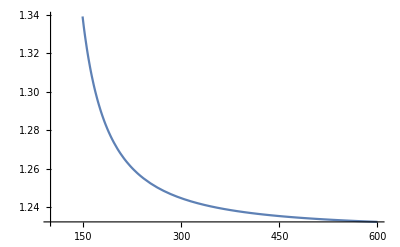

```mathematica
Plot[ncalc[x], {x, 100, 600}]
```

```mathematica
ncalc[128]
```

1.45641

```mathematica
kT = 2.18*10^-9;
kB = 1.380649*10^-23   ;
T = 83.81;
```

```mathematica
lray[x_] := 1/((8*Pi^3)/(3*x^4) *(((ncalc[x*10^9]*ncalc[x*10^9]-1)*(ncalc[x*10^9]*ncalc[x*10^9]+2))/3)^2*kB*T*kT);
```

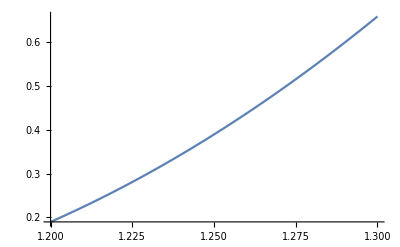

```mathematica
Plot[lray[x], {x, 1.2*10^-7, 1.3*10^-7}]
```

```mathematica
lray[128*10^-9]
```

```mathematica
0.5426119591443156

(*一、直接用折射率的上下限估计散射长度的误差*)
```

```mathematica
lray_mid= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((ncalc[128]*ncalc[128]-1)*(ncalc[128]*ncalc[128]+2))/3)^2*kB*T*kT)
lray_up= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(1/3((ncalc[128]+0.07)*(ncalc[128]+0.07)-1)*((ncalc[128]+0.07)*(ncalc[128]+0.07)+2))^2*kB*T*kT)
lray_down = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(1/3((ncalc[128]-0.07)*(ncalc[128]-0.07)-1)*((ncalc[128]-0.07)*(ncalc[128]-0.07)+2))^2*kB*T*kT)
```

0.542612

0.349314

0.88553

```mathematica
(*二、用三个a的上下限估计折射率以及散射长度的误差*)
nmid = ncalc[128]
nup = √((a0+0.09) + ((aUV+0.09)*128^2)/(128^2 - xUV^2)+((aIR+0.007)*128^2)/(128^2 - xIR^2))
ndown = √((a0-0.09) + ((aUV-0.09)*128^2)/(128^2 - xUV^2)+((aIR-0.007)*128^2)/(128^2 - xIR^2))
```

1.45641

1.58262

1.31816

```mathematica
lraymid= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((nmid*nmid-1)*(nmid*nmid+2))/3)^2*kB*T*kT)
lraydown = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((nup*nup-1)*(nup*nup+2))/3)^2*kB*T*kT)
lrayup = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((ndown*ndown-1)*(ndown*ndown+2))/3)^2*kB*T*kT)
```

0.542612

0.252117

1.52428

```mathematica
(*三、对折射率拟合公式求导计算误差*)
a10 = 1.24;
a20 = 0.27;
a30 = 0.00047;
a10err = 0.09;
a20err = 0.09;
a30err = 0.007;
Fray[a1, a2, a3] := √(a1 + (a2*128^2)/(128^2-106.6^2)+(a3*128^2)/(128^2-908.3^2));
D[Fray[a1, a2, a3], a1]
D[Fray[a1, a2, a3], a2]
D[Fray[a1, a2, a3], a3]
```

1/(2 √(a1+3.26346 a2-0.0202616 a3))

1.63173/(√(a1+3.26346 a2-0.0202616 a3))

-0.0101308/(√(a1+3.26346 a2-0.0202616 a3))

```mathematica
Frayerr = √((a10err/(2 √(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2+((1.6317294898455115*a20err)/(√(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2+(-(0.01013077893261485*a30err)/(√(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2)
```

0.105462

```mathematica
0.10546188244831425



(*Grace用到的LAr三相点折射率数据：1969 --> Root TF1 Fitting*)
```

```mathematica
(*Index of refraction, Rayleigh scattering length, and Sellmeier coefficients in solid and liquid argon and xenon*)

a0fit = 1.24526;
aUVfit = 2.65822/10;
aIRfit = 6.01569/10000;
xUV = 106.6;
xIR = 908.3;
ncalcfit[x_] := √(a0fit + (aUVfit*x^2)/(x^2 - xUV^2)+(aIRfit*x^2)/(x^2 - xIR^2));
```

```mathematica
ncalcfit[365]
```

1.23926

```mathematica
ncalc1[365]
```

1.23106

```mathematica
(*利用Grace硕士论文中的关联矩阵的方法计算误差 sigma=G^TVG*)
```

```mathematica
(*ROOT fitting results*)
```

```mathematica
G = {1/(2 √(a0fit+3.263458979691023 aUVfit-0.0202615578652297 aIRfit)), 1.6317294898455115/(√(a0fit+3.263458979691023 aUVfit-0.0202615578652297 aIRfit)),  -0.01013077893261485/(√(a0fit+3.263458979691023 aUVfit-0.0202615578652297 aIRfit))};
G
MatrixForm[#] &/@{G}
```

{0.34399,1.1226,-0.00696978}

{(0.34399
1.1226
-0.00696978)}

```mathematica
Cor = {{1.0, -0.9997894336993707, 0.8861402547735918}, {-0.9997894336993707, 1.0, -0.8777796122009764}, {0.8861402547735918,-0.8777796122009764, 1.0}};
MatrixForm[#] &/@{Cov}
```

```mathematica
{({{1., -0.9997894336993707, 0.8861402547735918}, {-0.9997894336993707, 1., -0.8777796122009764}, {0.8861402547735918, -0.8777796122009764, 1.}})};

Cor1 =  {{1.0, 0, 0}, {0, 1.0,0}, {0., 0. , 1.0}};

Cov = {{0.2515728609081064,-0.22980467457220466, 0.018505018449913715}, {-0.22980467457220466, 0.21000848574467648,-0.01674785042607267}, {0.018505018449913715,-0.01674785042607267, 0.0017334460304122442} };
Cov1 =  {{0.2515728609081064, 0, 0}, {0, 0.21000848574467648, 0}, {0, 0, 0.0017334460304122442}};
```

```mathematica
MatrixForm[#] &/@{Cov}
```

{(0.251573 | -0.229805 | 0.018505
-0.229805 | 0.210008 | -0.0167479
0.018505 | -0.0167479 | 0.00173345)}

```mathematica
GT = Transpose[{G}]
```

{{0.34399},{1.1226},{-0.00696978}}

```mathematica
G.Cov.GT
```

{0.117116}

```mathematica
√(G.Cov.GT)
```

{0.342222}

```mathematica
√(G.Cov1.GT)
```

{0.542611}

```mathematica
("Python curve_fit results")
```

```mathematica
a0p = 1.12191439;
a1p = 0.107380;
a2p = 0.00026354;
G1 = {1/(2 √(a0p+3.263458979691023 a1p-0.0202615578652297 a2p)), 1.6317294898455115/(√(a0p+3.263458979691023 a1p-0.0202615578652297 a2p)),  -0.01013077893261485/(√(a0p+3.263458979691023 a1p-0.0202615578652297 a2p))}
```

{0.412065,1.34476,-0.00834909}

```mathematica
Cov2 = {{2.01645949*10^-5,-1.84183801*10^-5, 1.48574357*10^-6},
{-1.84183801*10^-5, 1.68304047*10^-5,-1.34468027*10^-6},
{1.48574357*10^-6,-1.34468027*10^-6,1.39135600*10^-7} };
Cov2Unit = {{2.01645949*10^-5,0, 0},
{0, 1.68304047*10^-5,0},
{0, 0,1.39135600*10^-7} }
G1T = Transpose[{G1}]
```

{{0.0000201646,0,0},{0,0.0000168304,0},{0,0,1.39136×10^-7}}

{{0.412065},{1.34476},{-0.00834909}}

```mathematica
√(G1.Cov2.G1T)
```

{0.00366978}

```mathematica
√(G1.Cov2Unit.G1T)
```

{0.0058189}